## sig final: use only one eqn from the rank-1 matrix

```mathematica
Clear[sign,s,c,μ,B,v0];
sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]:=Block[{e=1,βinter =0,cond,cond1,cond2,matr,bc1,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,vdotk2,cs,λ1,a1,cost,θp,Dphase1,Dphase2,h1,vz1,zero1,ct1,ctct1,hzero1,hct1,hstcp1,hstsp1,colvec,mat,sol,sol1,sol2,Λ1,s1,int1},

kf1[θ_]=(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c);
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ]+2 c kf1[θ]^2;
h1[θ_]=1/Dphase1[θ]((vvec1[θ])[[3]]+ e B(bc1[θ].vvec1[θ]));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hct1 βintra}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ]/.sol,{θ,0,π}];
(*cond1=NIntegrate[int1[θ]/.sol1,{θ,0,π}];*)
cond2=NIntegrate[int1[θ]/.sol2,{θ,0,π}];
{B,cond2(*,cond,sol1,sol2,sol*)}
];
(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] *)
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
Quiet[sign[1,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop
```

{1,0.0000202499}

{{-55,0.0000202449},{-45,0.0000202471},{-35,0.0000202487},{-25,0.0000202498},{-15,0.0000202503},{-5,0.0000202502},{5,0.0000202496},{15,0.0000202485},{25,0.0000202468},{35,0.0000202445},{45,0.0000202417},{55,0.0000202383}}

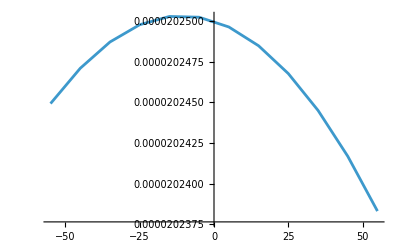

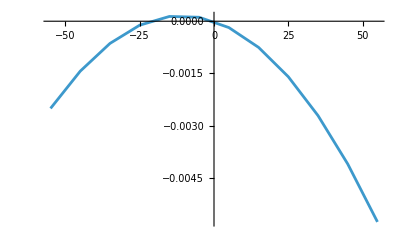

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
list=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-55,55,10}]
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
ListLinePlot[dat1]
x=1/Quiet[sig0[mu,cval,v0val,1,sval][[2]]];
dat2=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10},{i,1,len}];
ListLinePlot[dat2]
```

{{-55,2.52×10^-7},{-45,2.52×10^-7},{-35,2.52×10^-7},{-25,2.52×10^-7},{-15,2.52×10^-7},{-5,2.52×10^-7},{5,2.52×10^-7},{15,2.52×10^-7},{25,2.52×10^-7},{35,2.52×10^-7},{45,2.52×10^-7},{55,2.52×10^-7}}

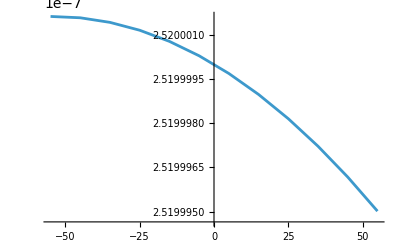

3.96825×10^6

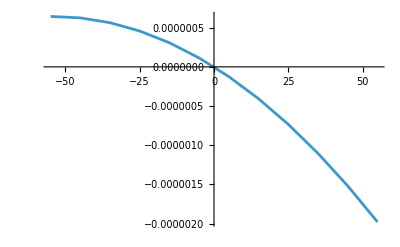

```mathematica
mu=10.0^-1; cval=5 10^-9 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
list=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-55,55,10}]
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
ListLinePlot[dat1]
x=1/Quiet[sig0[mu,cval,v0val,1,sval][[2]]];
dat2=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)1},{i,1,len}];
ListLinePlot[dat2]
```

## sigma at B=0

```mathematica
Clear[sig0,s,c,μ,B,v0];
sig0[μ_,c_,v0_,βintra_,s_]:=Block[{e=1,B=0,βinter =0,cond1,cond2,cond,matr,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vdotk1,cs,λ1,λ2,a1,a2,cost,θp,Dphase1,h1,vz1,h2,vz2,zero1,zero2,ct1,ctct1,hzero1,hct1,hct2,hstcp1,hstsp1,colvec,mat,sol,sol1,sol2,Λ1,s1,int1},

kf1[θ_]=(√(v0^2+4 c μ)-s v0)/(2 c);
Dphase1[θ_]=1;
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vdotk1[θ_]=2 c kf1[θ]^2+s v0 kf1[θ];
h1[θ_]=1/Dphase1[θ](2 c kf1[θ]+s v0 )Cos[θ];
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero1 βintra)}, {1/2 (hct1 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ]/.sol,{θ,0,π}];
cond1=NIntegrate[int1[θ]/.sol1,{θ,0,π}];
cond2=NIntegrate[int1[θ]/.sol2,{θ,0,π}];
{0,cond1,cond2,cond,sol1,sol2,sol}
];
(* sig0[μ_,c_,v0_,βintra_,s_] *)
mu=10.0^-0; cval=5 10^-5 ;v0val= 5 10^-4;sval=-1;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
```

{0,0.00020025,0.00020025,0.00011448,{λ1→0,a1→-0.00707549},{λ1→0,a1→-0.00707549},{λ1→0,a1→0.00201613}}

{0,0.00020025,0.00020025,0.000150143,{λ1→0,a1→-0.00707549},{λ1→0,a1→-0.00707549},{λ1→0,a1→-0.00176411}}

## linear k disp

```mathematica
Series[(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c),{c,0,1},Assumptions->{v0}∈Reals && v0>0]
%/.s->1
```

(v0-s v0)/(2 c)+(-B mbohr s+μ)/v0-((-B mbohr s+μ)^2 c)/v0^3+O[c]^2

(-B mbohr+μ)/v0-((-B mbohr+μ)^2 c)/v0^3+O[c]^2

```mathematica
Clear[sigs,s,c,μ,B,v0];
sigs[B_,μ_,v0_,βintra_,mbohr_,χ_]:=Block[{e=1,βinter =0,s=1,c=0,matr,bc1,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,vdotk2,cs,λ1,a1,cost,θp,Dphase1,Dphase2,h1,vz1,zero1,ct1,ctct1,hzero1,hct1,hstcp1,hstsp1,colvec,mat,cond1,cond2,cond,sol1,sol2,sol,Λ1,s1,int1},

kf1[θ_]=(-s B mbohr+μ)/v0;
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ];
h1[θ_]=1/Dphase1[θ]((vvec1[θ])[[3]]+ e B(bc1[θ].vvec1[θ]));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hct1 βintra}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ]/.sol,{θ,0,π}];
(*cond1=NIntegrate[int1[θ]/.sol1,{θ,0,π}];*)
cond2=NIntegrate[int1[θ]/.sol2,{θ,0,π}];
{B,cond2(*,cond,sol2,sol,sol1*)}
];
(* sigs[B_,μ_,v0_,βintra_,mbohr_,χ_] *)
mu=10.0^-1; v0val= 5 10^-3; omval=1 ; bohrrm=3*10^-7 ;
(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
sigs[10,mu,v0val,1,bohrrm,omval]
```

{10,0.0000249945}

```mathematica
Clear[sigs0,s,c,μ,B,v0];
sigs0[μ_,v0_,βintra_]:=Block[{e=1,B=0,βinter =0,s=1,c=0,matr,bc1,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,vdotk2,cs,λ1,a1,cost,θp,Dphase1,Dphase2,h1,vz1,zero1,ct1,ctct1,hzero1,hct1,hstcp1,hstsp1,colvec,mat,cond1,cond2,cond,sol1,sol2,sol,Λ1,s1,int1},

kf1[θ_]=μ/v0;
bc1[θ_]={0,0,0};
Dphase1[θ_]=1 ;
vvec1[θ_]= (s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ];
h1[θ_]=1/Dphase1[θ]((vvec1[θ])[[3]]+ e B(bc1[θ].vvec1[θ]));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hct1 βintra}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol2=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ]/.sol,{θ,0,π}];
cond1=NIntegrate[int1[θ]/.sol1,{θ,0,π}];
cond2=NIntegrate[int1[θ]/.sol2,{θ,0,π}];
{0,cond2,cond,cond1,sol2,sol,sol1}
(* sol1 does not work for finite B *)
];
(* sigs[B_,μ_,v0_,βintra_,mbohr_,χ_] *)
mu=10.0^-1; v0val= 5 10^-3; omval=1 ; bohrrm=3*10^-7 ;
(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
Quiet[sigs0[mu,v0val,1]]
```

{0,0.000025,0.0000139881,0.000025,{λ1→2.50722×10^-19,a1→-0.0025},{λ1→0.,a1→0.000803571},{λ1→2.50722×10^-19,a1→-0.0025}}

```mathematica
mu=10.0^-1; v0val= 5 10^-3; omval=1 ; bohrrm=0 ;
Quiet[sigs0[mu,v0val,1]]
Quiet[sigs[0.01,mu,v0val,1,bohrrm,omval]]//Chop
```

{0,0.000025,0.0000154762,0.000025,{λ1→2.1684×10^-19,a1→-0.0025},{λ1→0.,a1→0.000357143},{λ1→2.1684×10^-19,a1→-0.0025}}

{0.01,0.000025}

{{-55,0.0000248347},{-45,0.0000248893},{-35,0.000024933},{-25,0.0000249658},{-15,0.0000249877},{-5,0.0000249986},{5,0.0000249986},{15,0.0000249877},{25,0.0000249658},{35,0.000024933},{45,0.0000248893},{55,0.0000248347}}

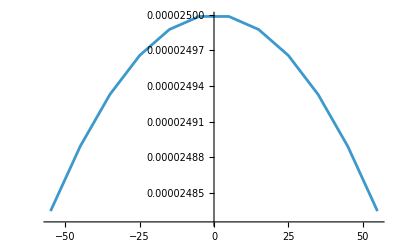

{0,0.000025,0.0000154762,0.000025,{λ1→2.1684×10^-19,a1→-0.0025},{λ1→0.,a1→0.000357143},{λ1→2.1684×10^-19,a1→-0.0025}}

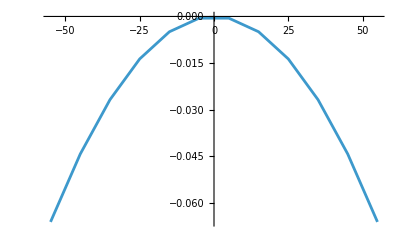

```mathematica
mu=10.0^-1; v0val= 5 10^-3; omval=1 ; bohrrm=0 ;
sval=1;
list=Table[Quiet[sigs[B,mu,v0val,1,bohrrm,omval]]//Chop,{B,-55,55,10}]
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
ListLinePlot[dat1]
Quiet[sigs0[mu,v0val,1]]

x=1/%[[2]];
dat2=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10},{i,1,len}];
ListLinePlot[dat2]
```